## Sample crediblePlot notebook

### Plot options

```mathematica
SetOptions[#,Frame->True,FrameStyle->Directive[Black,18,FontFamily->Times,Thickness[.004]],AspectRatio->1,PlotStyle->Thick,ImageSize->400]&@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot,RegionPlot};
logSpace[a_, b_, n_] := 10.0^Range[Log10[a], Log10[b], (Log10[b] - Log10[a])/(n - 1)];
```

### Set up CrediblePlot

#### **First time setup, please read**

I suggest you place crediblePlot in a path known to mathematica, you can check the paths mathematica searches using:

```mathematica
$Path
```

{/usr/local/Wolfram/Mathematica/11.0/SystemFiles/Links,/home/jay/.Mathematica/Kernel,/home/jay/.Mathematica/Autoload,/home/jay/.Mathematica/Applications,/usr/share/Mathematica/Kernel,/usr/share/Mathematica/Autoload,/usr/share/Mathematica/Applications,.,/home/jay,/usr/local/Wolfram/Mathematica/11.0/AddOns/Packages,/usr/local/Wolfram/Mathematica/11.0/SystemFiles/Autoload,/usr/local/Wolfram/Mathematica/11.0/AddOns/Autoload,/usr/local/Wolfram/Mathematica/11.0/AddOns/Applications,/usr/local/Wolfram/Mathematica/11.0/AddOns/ExtraPackages,/usr/local/Wolfram/Mathematica/11.0/SystemFiles/Kernel/Packages,/usr/local/Wolfram/Mathematica/11.0/Documentation/English/System,/usr/local/Wolfram/Mathematica/11.0/SystemFiles/Data/ICC,/home/jay/Physics/Codes/CrediblePlot}

use one of the above folders, or add the folder where you keep crediblePlot with (replace with your directory first):

```mathematica
userPath="/home/jay/Physics/Codes/CrediblePlot";
```

```mathematica
If[ValueQ[userPath],Import[FileNameJoin[{$UserBaseDirectory,"Kernel","init.m"}],"Text"]<>"\n\nAppendTo[$Path,\""<>userPath<>"\"];"//Export[FileNameJoin[{$UserBaseDirectory,"Kernel","init.m"}],#,"Text"]&;Exit[];,Print["Please set userPath first"];];
```

#### To load CrediblePlot

You can now load crediblePlot in any notebook with (or alternatively add to your init.m file) :

```mathematica
<<"crediblePlot.m"
```

### Bivariate gaussian example

Using a bivariate gaussian distribution with no covariance:

```mathematica
f[x_,y_]:= PDF[NormalDistribution[0,1],x]PDF[NormalDistribution[5,1],y];
```

```mathematica
data=ParallelTable[x=RandomReal[10]-5;y=RandomReal[10];{x,y,f[x,y]},{n,1,10^6}];
```

CrediblePlot takes probability samples **not probability density samples** so we must normalize this data:

```mathematica
data[[All,3]]/=Plus@@data[[All,3]];
```

#### The 1D marginal posteriors

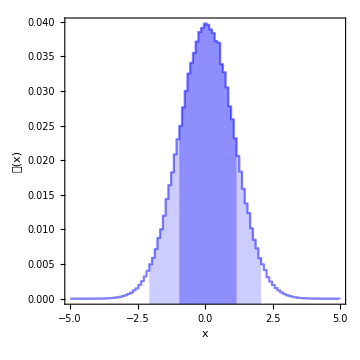
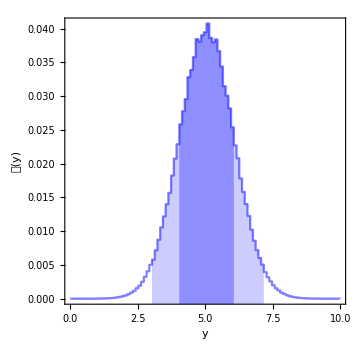

```mathematica
{CrediblePlot1D[data[[All,{1,3}]],NumBins->100,FrameLabel->{"x","𝒫(x)"}],CrediblePlot1D[data[[All,{2,3}]],NumBins->100,FrameLabel->{"y","𝒫(y)"}]}
```

#### The 2D marginal posterior

By default Credible regions are 1 and 2σ, shaded and have no smoothing applied:

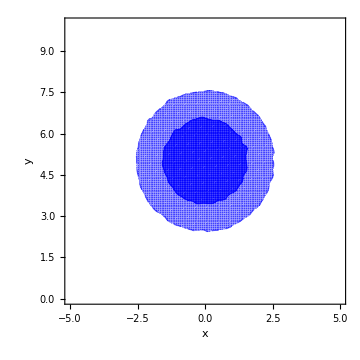

```mathematica
CrediblePlot2D[data,NumBins->50,FrameLabel->{"x","y"}]
```

Show a single contour at 90% credible level with smoothing:

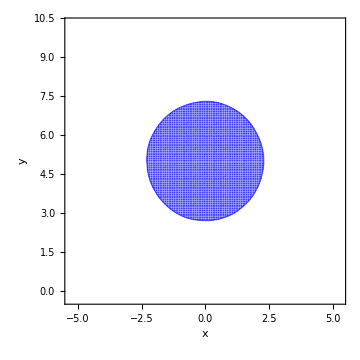

```mathematica
CrediblePlot2D[data,NumBins->50,CredibleLevel->0.9,Smoothing->True,FrameLabel->{"x","y"}]
```

You can choose to show the density instead of shading:

```mathematica
CrediblePlot2D[data,NumBins->50,Smoothing->True,ShowDensity->True,FrameLabel->{"x","𝒫(x)"}]
```

-Graphics-

Show the maximum probability point:

```mathematica
CrediblePlot2D[data,NumBins->50,Smoothing->True,ShowDensity->True,MaxPoint->True,FrameLabel->{"x","𝒫(x)"}]
```

-Graphics-

### Example on log scale

Using a bivariate gaussian distribution with covariance:

```mathematica
μx=1600;σx=600;
μy=500;σy=50;
ρ=.5;
```

```mathematica
f[x_,y_]:= Exp[-(x-μx)^2/σx^2-(y-μy)^2/σy^2+(2ρ(x-μx)(y-μy))/(σx σy)];
```

Generate some random data:

```mathematica
data=ParallelTable[x=10^RandomReal[4];y=10^RandomReal[3];{x,y,f[x,y]},{n,1,10^6}];
```

Normalize the data:

```mathematica
data[[All,3]]/=Plus@@data[[All,3]];
```

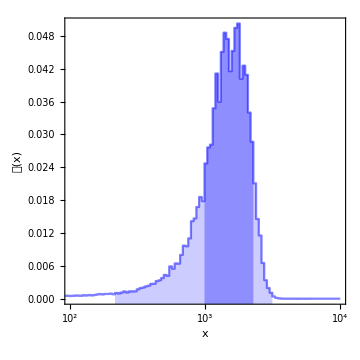

```mathematica
LogCrediblePlot1D[data[[All,{1,3}]],NumBins->200,PlotRange->{{100,10^4},All},FrameLabel->{"x","𝒫(x)"}]
```

SimPoint can be used to show the simulated or ideal mean of the distribution:

{{1,4},{2,All},{0,1}}

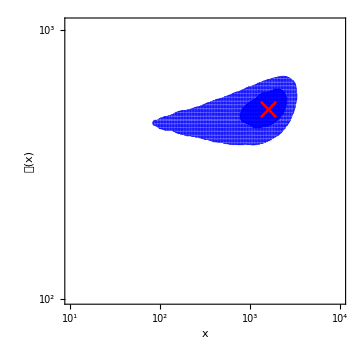

```mathematica
LogLogCrediblePlot2D[data,NumBins->200,Smoothing->True,PlotRange->{{10,10^4},{100,All},{0,1}},SimPoint->{1600,500},FrameLabel->{"x","y"}]
```

### Example of bimodal distribution

```mathematica
μx1=3;μx2=-3;σx=1;
μy1=3;μy2=-3;σy=1;
```

```mathematica
f[x_,y_]:= Exp[-(x-μx1)^2/σx^2-(y-μy1)^2/σy^2]+Exp[-(x-μx2)^2/σx^2-(y-μy2)^2/σy^2];
```

Generate some random data:

```mathematica
data=ParallelTable[RandomReal[{-8,8},2]//Append[#,f@@#]&,{n,1,10^6}];
data[[All,3]]/=Plus@@data[[All,3]];
```

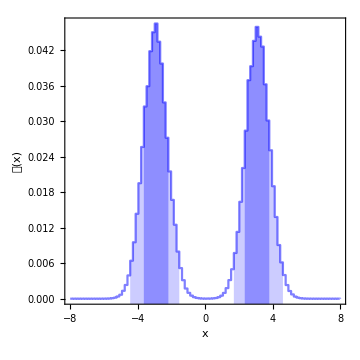

```mathematica
CrediblePlot1D[data[[All,{1,3}]],NumBins->100,FrameLabel->{"x","𝒫(x)"}]
```

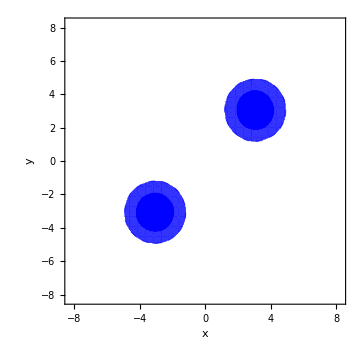

```mathematica
CrediblePlot2D[data,NumBins->100,FrameLabel->{"x","y"},Smoothing->True]
```

### Example with corner plot

```mathematica
μM={0,0,0};
```

```mathematica
InvΣ={{1,-.5,.1},{-.5,1,.4},{.1,.4,1}}//Inverse;
```

```mathematica
detInvΣ=Det[Inverse[InvΣ]];
```

```mathematica
fMulti[x_]:= 1/(√((2π)^3 detInvΣ))Exp[-1/2(x-μM).InvΣ.(x-μM)];
```

This function was designed for use with MultiNest output in mind, and so it takes rows with {P,-2logL, x1,x2,...,xN}:

```mathematica
data=ParallelTable[RandomReal[{-3,3},3]//Join[{fMulti[#],-2Log[fMulti[#]]},#]&,{n,1,10^6}];
data[[All,1]]/=Plus@@data[[All,1]];
```

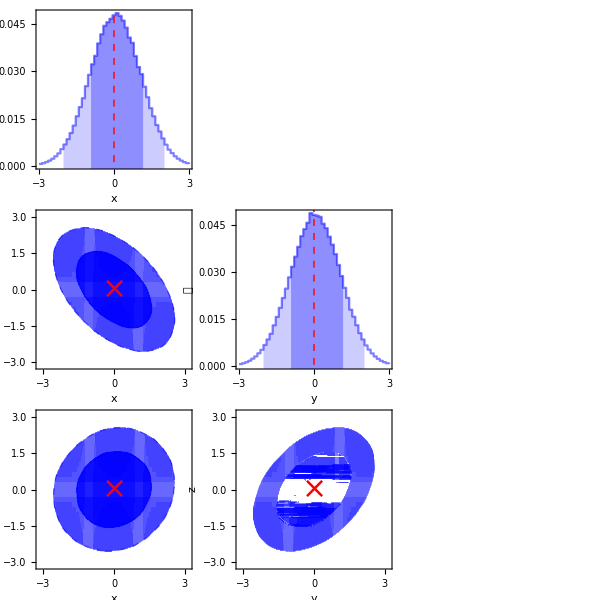

```mathematica
CornerPlot[data,{"x","y","z"},SimPoint->{0,0,0}]
```